```mathematica
c=4.0;(*concentration parameter*)
M200=20*10^14;(*solar mass*)
G=4.302*10^-9;(*wiki*)
DL=946.008;(*Mpc*)
DLS=1291.24;
DS=1783.21;
Hz=67.8;(*Hubble constant*)
r200=((G×M200)/(100×Hz^2))^(1/3);
rs = r200/c;
deltac=200/3 c^3/(Log[1+c]-c/(1+c));
Sigmac = ((3×10^5)^2)/(4×Pi×G)DS/(DLS×DL);
rouc = 3 Hz^2/(8×Pi×G);
```

0.663774

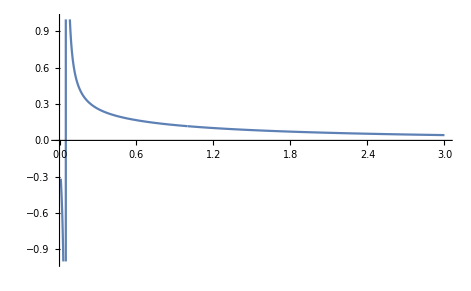

```mathematica
F1[x_]:=Piecewise[{{(4ArcTanh[√((1-x)/(1+x))])/(x^2 √(1-x^2))+(2 Log[x/2])/x^2-1/(x^2-1)+(2ArcTanh[√((1-x)/(1+x))])/((x^2-1)√(1-x^2)),x<1},{2Log[1/2]+5/3,x==1},
{(4ArcTan[√((x-1)/(x+1))])/(x^2×√(x^2-1))+(2 Log[x/2])/x^2-1/(x^2-1)+(2ArcTan[√((x-1)/(x+1))])/((x^2-1)^(3/2)),x>1}}];
Gmma[x_]:=(2×rs ×deltac ×rouc)/Sigmac F1[x];
F2[x_]:=Piecewise[{{1/(x^2-1)(1-(2ArcTanh[√((1-x)/(1+x))])/(√(1-x^2))),x<1},{1/3,x==1},
{1/(x^2-1)(1-(2ArcTan[√((x-1)/(x+1))])/(√(x^2-1))),x>1}}];
Kappa[x_]:=(2×rs ×deltac× rouc)/Sigmac F2[x];
g[x_]:=Gmma[x]/(1-Kappa[x]);
rs
Plot[g[x],{x,0.01,3}, PlotRange->{-1,1}]
```

```mathematica
(*r=(1069*0.03)/3600*Pi/180*DL (*Mpc*)
xvar=r/rs*)
g[xvar]
```

0.147085

0.279185

0.189651

```mathematica
FindRoot[g[a]==0.07,{a,0.1}]
```

{a→1.87093}

```mathematica
x0=1.870929034448965;(*dimentionless radius factor*)
R_Mpc=rs*x0                                                   (*grid radius in Mpc*)
R_px=(x0*rs*180/Pi*3600)/DL*1/0.03     (*grid radius in pixel - HST scale*)
```

1.24187

9025.82

```mathematica
?Log
```

RowBox[{"Log", "[", StyleBox["z", "TI"], "]"}] gives the natural logarithm of StyleBox["z", "TI"] (logarithm to base StyleBox["e", "TI"]). 
RowBox[{"Log", "[", RowBox[{StyleBox["b", "TI"], ",", StyleBox["z", "TI"]}], "]"}] gives the logarithm to base StyleBox["b", "TI"].

```mathematica
Names["Global`*"]
```

{c,deltas,DL,F1,G,Global,Gmma,M200,Name,rous,rs,Sigmas,W,Wh,who,Who,Whos,x,x$}

```mathematica
a
```

a

```mathematica
Remove["c","deltas","DL","F1","G"]
```

```mathematica
Delete[a]
```

Delete[a]

```mathematica
6144*0.065*Pi/180/3600*946.326
```

1.83223

```mathematica
1.83223/rs
```

3.47779

```mathematica
Integrate[x^2/(x(x+1)^2),{x,0.01,3.48}]
```

0.722788